# Dropbox

```mathematica
dropbox=ServiceConnect["Dropbox","New"]
```

ServiceObject[…]

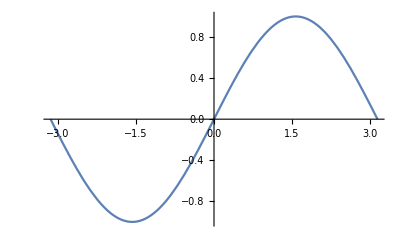

```mathematica
plot=Plot[Sin[x],{x,-Pi,Pi}]
```

### Upload a file

```mathematica
ServiceExecute[dropbox,"GraphicsUpload",{"Path"->"/Screenshots/plot_sin.jpg","Graphics"->plot}]
```

{Modified→Missing[KeyAbsent,modified],Revision→Missing[KeyAbsent,revision],Rev→Missing[KeyAbsent,rev],Path→Missing[KeyAbsent,path],Root→Missing[KeyAbsent,root],MimeType→Missing[KeyAbsent,mime_type]}

```mathematica
dropbox["FileNames","Path"->"Screenshots"]//Short
```

{/Screenshots/51lp4dJUWbL.jpg,/Screenshots/.png,/Screenshots/A.Natures.Weirdest 1.jpg,«253»,/Screenshots/Wolfram,/Screenshots/wooden_camera.png}

### Downloading a file

```mathematica
ServiceExecute[dropbox,"FileContents",{"root"->"dropbox","Path"->"/Screenshots/Screenshot 2015-02-05 16.11.00.png"}]
```

```mathematica
ServiceExecute[dropbox,"ImportFile",{"root"->"dropbox","Path"->"/Screenshots/51lp4dJUWbL.jpg"}]
```

-Graphics-

### Deleting a file

```mathematica
ServiceExecute[dropbox,"RawFileDelete",{"root"->"dropbox","Path"->"/Screenshots/sinplot.jpg"}]
```